# HONEYCOMB ARMcHAIr

```mathematica
ClearAll["Global`*"]
```

```mathematica
matrixhexagonal=({{w-λ, Ω  f, 0, -Ω f}, {Ω  SuperStar[f], w-λ, -Ω SuperStar[f], 0}, {0, Ω f, -w-λ, -Ω f}, {Ω  SuperStar[f], 0, -Ω SuperStar[f], -w-λ}});
eq=ComplexExpand[Det[matrixhexagonal],TargetFunctions->{Abs}]
Solve[eq==0,λ]
qq={kx,ky};
e1.qq;
```

w^4-2 w^2 λ^2+λ^4-4 f w^2 Ω^2 f^*

{{λ→-√(w^2-2 √f w Ω √(f^*))},{λ→√(w^2-2 √f w Ω √(f^*))},{λ→-√(w^2+2 √f w Ω √(f^*))},{λ→√(w^2+2 √f w Ω √(f^*))}}

```mathematica
co[j_,θ_,ϑ_]:=1-3 Sin[θ]^2 Cos[ϑ-(2π)/3(j-1)]^2;
(*θ=(0Pi/180);
N[θ]/Degree;*)
ϑ=(0Pi/180);(*armchair*)
N[ϑ]/Degree;
co[1,θ,ϑ]
co[2,θ,ϑ]
co[3,θ,ϑ]
f[θ_]:=co[1,θ,ϑ]Exp[I (e1.qq)]+co[2,θ,ϑ]Exp[I (e2.qq)]+co[2,θ,ϑ]Exp[I (e3.qq)]
f[θ]
p=100;
e1={0,-1}; e2={(√3)/2,1/2};e3={(-√3)/2,1/2};
```

1-3 Sin[θ]^2

1-(3 Sin[θ]^2)/4

1-(3 Sin[θ]^2)/4

ⅇ^(ⅈ e1.{kx,ky}) (1-3 Sin[θ]^2)+ⅇ^(ⅈ e2.{kx,ky}) (1-(3 Sin[θ]^2)/4)+ⅇ^(ⅈ e3.{kx,ky}) (1-(3 Sin[θ]^2)/4)

```mathematica
fxx[θ_]:=ComplexExpand[Re[f[θ]]]
fyy[θ_]:=ComplexExpand[Im[f[θ]]]
ff[θ_]:=Simplify[fxx[θ]^2+fyy[θ]^2]
E1[θ_,kx_,ky_]:=1+t √ff[θ];
E2[θ_,kx_,ky_]:=1-t √ff[θ];
```

```mathematica
ff[0]
E1[0,kx,ky]
```

3+2 Cos[√3 kx]+2 Cos[1/2 (√3 kx-3 ky)]+2 Cos[1/2 (√3 kx+3 ky)]

1+t √(3+2 Cos[√3 kx]+2 Cos[1/2 (√3 kx-3 ky)]+2 Cos[1/2 (√3 kx+3 ky)])

```mathematica
t=0.01;
b=Show[Plot3D[E1[0,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->p,PlotStyle->Directive[Opacity[0.7],Yellow,Specularity[White,50]],Mesh->None],Plot3D[E2[0,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->p,PlotStyle->Directive[Red,Opacity[0.7]],Mesh->None],AxesLabel->{Style[Subscript[q,x]."a",Large],Style[Subscript[q,y]."a",Large],Style[Subscript[w,q]^"±"/Subscript[w,0],Large]},PlotLabel->"Collective plasmon dispersion for the out of plane θ=0",Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},LabelStyle->Directive[Black,FontSize->24],
PlotRange->All];
a=Show[ContourPlot[E1[0,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->"Rainbow"],ContourPlot[E2[0,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->"Rainbow"],
PlotRange->All,
Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,ColorFunction->"Rainbow"];

level=0.97;gr=Graphics3D[{Texture[a],EdgeForm[],Polygon[{{-Pi,-Pi,level},{Pi,-Pi,level},{Pi,Pi,level},{-Pi,Pi,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}];

Show[b,gr,PlotRange->All,PlotLegends->Automatic,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ky=0;t=0.01;
b=Show[Plot3D[E1[θ,kx,ky],{kx,-π,π},{θ,0,π/2},PlotPoints->p,PlotStyle->Directive[Opacity[0.7],Pink,Specularity[White,50]],MeshStyle->None],Plot3D[E2[θ,kx,ky],{kx,-π,π},{θ,0,π/2},PlotPoints->p,LabelStyle->Directive[Large,Bold],PlotStyle->Directive[Opacity[0.7],Yellow,Specularity[White,50]],MeshStyle->None],AxesLabel->{Style[Subscript[q,x]."a",Large],Style[Subscript[q,y]."a",Large],Style[Subscript[w,q]^"±"/Subscript[w,0],Large]},Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0, π/4,π/2},Automatic},PlotLabel->Style["Collective plasmon dispersion K-Γ-K' ϑ = 0°  "],
PlotRange->All];
Show[b,PlotRange->All,BoxRatios->{1,1,1},LabelStyle->Directive[Larger,FontFamily->"Helvetica"]]
```

-Graphics3D-

```mathematica
E1[0,kx,ky]
```

1+0.01 √(5+4 Cos[(3 ky)/2])

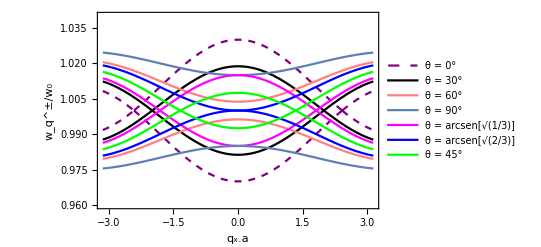

```mathematica
t=0.01;ky=0;
h=Show[Plot[{E1[0,kx,ky]},{kx,-π,π},PlotStyle->{Purple,Thick,Dashed}],
Plot[E2[0,kx,ky],{kx,-π,π},PlotStyle->{Purple,Thick,Dashed},PlotLegends->{"θ = 0°"},LabelStyle->Directive[Black,FontSize->18]],Plot[{E1[Pi/6,kx,ky]},{kx,-π,π},PlotStyle->{Black,Thick}],Plot[{E2[Pi/6,kx,ky]},{kx,-π,π},PlotStyle->{Black,Thick},PlotLegends->{"θ = 30°"},LabelStyle->Directive[Black,FontSize->18]],Plot[{E1[Pi/3,kx,ky]},{kx,-π,π},PlotStyle->{Pink,Thick}],
Plot[E2[Pi/3,kx,ky],{kx,-π,π},PlotStyle->{Pink,Thick},PlotLegends->{"θ = 60°"},LabelStyle->Directive[Black,FontSize->18]],Plot[{E1[Pi/2,kx,ky]},{kx,-π,π},PlotStyle->{Thick},PlotLegends->{"θ = 90°"},LabelStyle->Directive[Black,FontSize->18]],Plot[{E1[ArcSin[√(1/3)],kx,ky]},{kx,-π,π},PlotStyle->{Thick,Magenta},PlotLegends->{"θ = arcsen[√(1/3)]"},LabelStyle->Directive[Black,FontSize->18]],Plot[{E2[ArcSin[√(1/3)],kx,ky]},{kx,-π,π},PlotStyle->{Thick,Magenta}],Plot[{E1[ArcSin[√(2/3)],kx,ky]},{kx,-π,π},PlotStyle->{Thick,Blue},PlotLegends->{"θ = arcsen[√(2/3)]"},LabelStyle->Directive[Black,FontSize->18]],Plot[{E2[ArcSin[√(2/3)],kx,ky]},{kx,-π,π},PlotStyle->{Thick,Blue}],Plot[{E2[Pi/2,kx,ky]},{kx,-π,π},PlotStyle->{Thick}],Plot[{E1[Pi/4,kx,ky]},{kx,-π,π},PlotStyle->{Thick,Green},PlotLegends->{"θ = 45°"},LabelStyle->Directive[Black,FontSize->18]],Plot[{E2[Pi/4,kx,ky]},{kx,-π,π},PlotStyle->{Thick,Green}],
Frame->True,PlotRange->{{-Pi,Pi},{0.96,1.04}},LabelStyle->Directive[Black,FontSize->18],AxesLabel->{Style[Subscript[q,x ]."a",Large],Style[Subscript[w,q]^"±"/Subscript[w,0],FontSize->32]}]
```

```mathematica
ClearAll["Global`*"]
e1={0,-1}; e2={(√3)/2,1/2};e3={(-√3)/2,1/2};
qq={kx,ky};
e1.qq
co[j_,θ_,ϑ_]:=1-3 Sin[θ]^2 Cos[ϑ-(2π)/3(j-1)]^2;
(*θ=(0Pi/180);
N[θ]/Degree;*)
ϑ=(0Pi/180);
N[ϑ]/Degree;
co[1,θ,ϑ]
co[2,θ,ϑ]
co[3,θ,ϑ]
f[θ_]:=co[1,θ,ϑ]Exp[I (e1.qq)]+co[2,θ,ϑ]Exp[I (e2.qq)]+co[2,θ,ϑ]Exp[I (e3.qq)]
f[θ]
p=100;
```

-ky

1-3 Sin[θ]^2

1-(3 Sin[θ]^2)/4

1-(3 Sin[θ]^2)/4

ⅇ^(-ⅈ ky) (1-3 Sin[θ]^2)+ⅇ^(ⅈ (-(√3 kx)/2+ky/2)) (1-(3 Sin[θ]^2)/4)+ⅇ^(ⅈ ((√3 kx)/2+ky/2)) (1-(3 Sin[θ]^2)/4)

```mathematica
fx[θ_]:=ComplexExpand[Re[f[θ]]]
fy[θ_]:=ComplexExpand[Im[f[θ]]]
ff[θ_]:=Simplify[fx[θ]^2+fy[θ]^2]
E1[θ_,kx_,ky_]:=1+t √ff[θ];
E2[θ_,kx_,ky_]:=1-t √ff[θ];
```

```mathematica
kx=0;t=0.01;
b=Show[Plot3D[E1[θ,kx,ky],{ky,-π,π},{θ,0,π/2},PlotPoints->p,PlotStyle->Directive[Opacity[0.7],Pink,Specularity[White,50]],MeshStyle->None],Plot3D[E2[θ,kx,ky],{ky,-π,π},{θ,0,π/2},PlotPoints->p,LabelStyle->Directive[Large,Bold],PlotStyle->Directive[Opacity[0.7],Yellow,Specularity[White,50]],MeshStyle->None],AxesLabel->{Style[Subscript[q,x]."a",Large],Style[Subscript[q,y]."a",Large],Style[Subscript[w,q]^"±"/Subscript[w,0],Large]},Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0, π/4,π/2},Automatic},PlotLabel->Style["Collective plasmon dispersion M-Γ-M' ϑ = 0°"],
PlotRange->All];
Show[b,PlotRange->All,BoxRatios->{1,1,1},LabelStyle->Directive[Larger,FontFamily->"Helvetica"]]
```

-Graphics3D-

```mathematica
t=0.01;
b=Show[Plot3D[E1[Pi/4,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->p,PlotStyle->Directive[Opacity[0.7],Yellow,Specularity[White,50]],Mesh->None],Plot3D[E2[Pi/4,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->p,PlotStyle->Directive[Red,Opacity[0.7]],Mesh->None],AxesLabel->{Style[Subscript[q,xa],Large,Bold],Style[Subscript[q,ya],Large,Bold],Style[Subscript[w,q]^"±"/w0,Large,Bold]},PlotLabel->"Collective plasmon dispersion θ=45 ϑ = 0°",
PlotRange->All];
a=Show[ContourPlot[E1[Pi/4,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->"Rainbow"],ContourPlot[E2[Pi/4,kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->"Rainbow"],
PlotRange->All,
Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,ColorFunction->"Rainbow"];

level=0.97;gr=Graphics3D[{Texture[a],EdgeForm[],Polygon[{{-Pi,-Pi,level},{Pi,-Pi,level},{Pi,Pi,level},{-Pi,Pi,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}];

Show[b,gr,PlotRange->All,PlotLegends->Automatic,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
t=0.01;
b=Show[Plot3D[E1[ArcSin[√(2/3)],kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->220,PlotStyle->Directive[Opacity[0.7],Yellow,Specularity[White,50]],Mesh->None],Plot3D[E2[ArcSin[√(2/3)],kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->p,PlotStyle->Directive[Red,Opacity[0.7]],Mesh->None],AxesLabel->{Style[Subscript[q,xa],Large,Bold],Style[Subscript[q,ya],Large,Bold],Style[Subscript[w,q]^"±"/w0,Large,Bold]},PlotLabel->"Collective plasmon dispersion θ=ArcSin[√(2/3)] ϑ = 0°",
PlotRange->All];
a=Show[ContourPlot[E1[ArcSin[√(2/3)],kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->"Rainbow"],ContourPlot[E2[ArcSin[√(2/3)],kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},ColorFunction->"Rainbow"],
PlotRange->All,
Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,ColorFunction->"Rainbow"];

level=0.97;gr=Graphics3D[{Texture[a],EdgeForm[],Polygon[{{-Pi,-Pi,level},{Pi,-Pi,level},{Pi,Pi,level},{-Pi,Pi,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}];

Show[b,gr,PlotRange->All,PlotLegends->Automatic,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
E1[ArcSin[√(1/3)],kx,ky]
E2[ArcSin[√(1/3)],kx,ky]
```

1+3/2 t √(Cos[(√3 kx)/2]^2)

1-3/2 t √(Cos[(√3 kx)/2]^2)

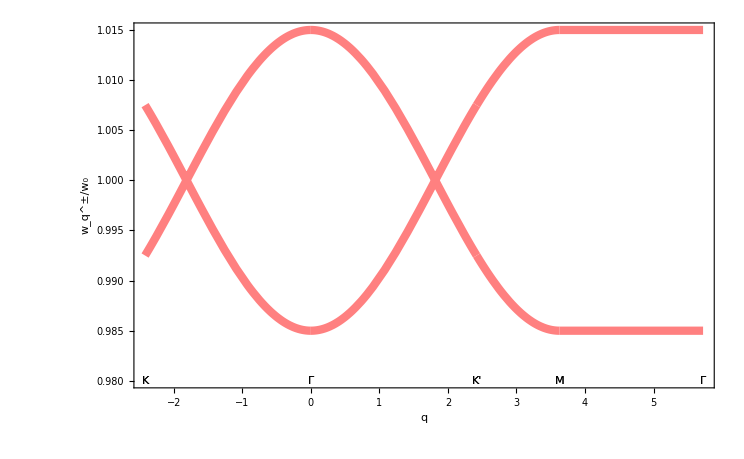

```mathematica
W1[kx_,ky_]:=1+3/2 t √(Cos[(√3 kx)/2]^2)
W2[kx_,ky_]:=1-3/2 t √(Cos[(√3 kx)/2]^2)
M=(2Pi)/3; PK=(2Pi)/(3 √3);;KZ=2M/√3;t=0.01;
Γp={0,0.98};M1point={M,0.98};M2point={M/2,Pi/(√3)};KP={(M+PK),0.98};
KP2={(M+PK+2PK),0.98};KP0={(-KZ),0.98};KP1={(KZ),0.98};KP3={(KZ+PK),0.98};

zb=ListPlot[{{KP0},{Γp},{KP1},{KP3},{KP2}},PlotMarkers->{"K","Γ","K'","M","Γ"},PlotStyle->{Black,Black,Black}];
ba=Plot[{If[0>q>-KZ,{W1[q,0],W2[q,0]}],If[0<q<KZ,{W1[q,0],W2[q,0 ]}],If[KZ<q<KZ+PK,{W1[q,0],W2[q,0 ]}],If[(KZ+PK)<q<(PK+KZ+M),{W1[KZ+PK,q-(KZ+PK)],W2[KZ+PK,q-(KZ+PK)]}]},{q,-KZ,(PK+M+KZ)},PlotRange->Full,PlotStyle->{{Thickness[0.008],Pink},{Thickness[0.008],Pink},{Thickness[0.008],Pink}},GridLines->{{-KZ,KZ,PK+KZ,PK+M+KZ}},AxesLabel->{Style[q,Bold,Large],Style[Subscript[w,q]^"±"/Subscript[w,0],Large]},LabelStyle->Directive[Black,FontSize->22]];
Show[ba,zb,PlotRange->All,Frame->True]
```